# Project Coding Template APPM 2350 : Spring 2017 Authors: This student That student The student

Hi everyone!
The purpose of this document is to show you how a Mathematica notebook can be organized for easier legibility. It might make it is easier to understand the flow of your work this way.

For the 1st project I recommend copying the coaster template code into the first section below and starting by reviewing the Crash Course file!

```mathematica
Clear["Global`*"]
```

## Section 3: Observers at three different latitudes

Some text here to explain the following code (notice the brackets on the right→ side of the page!)
Also use SHIFT ENTER to evaluate code. If it goes blue to black, then it’s been saved.

```mathematica
Θ[t_] := -0.41 * Cos[(2π*t)/ 365.25]
```

```mathematica
x[t_,ϕ_] := Cos[ϕ] * Sin[2π*t]
```

```mathematica
y[t_,ϕ_] := -Cos[ϕ] * Cos[2π*t] * Cos[Θ[t]] + Sin[ϕ] * Sin[Θ[t]]
```

```mathematica
z[t_, ϕ_] := Cos[ϕ] * Cos[2π * t] * Sin[Θ[t]] + Sin[ϕ] * Cos[Θ[t]]
```

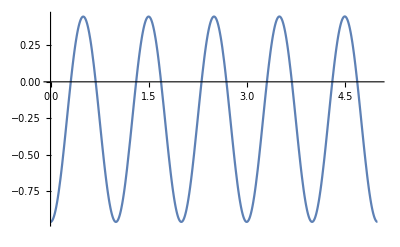

```mathematica
Plot[{y[t,0.698132]},{t,0,5}]
```

```mathematica
days ={t} /. Table[FindRoot[y[t,0.698132]==0, {t, day -0.25}], {day, 0.5, 365,0.5}];
```

```mathematica
For[i = 0, i < 364, i+2, l =days[[i+1]] - days[[i]]; If[l > max, max = l]; If[l < min, min = l]; Print[l]]
```

{0.309413-List}

{0.309413-List}

{0.309413-List}

«539 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«10 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«10 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«11 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«10 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«10 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«10 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«177 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«9 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«9 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«9 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«11 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«10 more identical outputs»

$Aborted

{0.309413-List}

{0.309413-List}

{0.309413-List}

«665 more identical outputs»

```mathematica
RiseAngle[dayRA_,phiRA_] := 
(srtRA = FindRoot[y[tRA, phiRA] == 0, {tRA, Round[dayRA] -0.75}];
180*ArcCos[n[tRA/.srtRA,phiRA]]/Pi)
```

```mathematica
boulderRA = Table[RiseAngle[dayRA,40*Pi/180],{dayRA,0,365,1}];
```

## Section II: Honey Badgers

Explaining more code

```mathematica
g[x_]=f'[x];
h[x_]=a-2g[x];
Plot[h[x],{x,-1,1},
PlotLabel->Style["Hello Out There!",Large],
AxesLabel->{"X label (meters)","Y label (meters)"},
ImageSize->Large]
```

-Graphics-

### Sub-Section Analysis

```mathematica
FindRoot[h[x],{x,0.1}]
```

FindRoot::nlnum: The function value {a-2. f'[0.1]} is not a list of numbers with dimensions {1} at {x} = {0.1}.

FindRoot[h[x],{x,0.1}]

A little more text, just for good measure.